```mathematica
alphabeta[a_,b_,c_,d_,aa_,bb_]:={
-c/(a*aa+b),
(d-a*bb)/(a*aa+b)
};
TridiagonalSolve[A_,d_]:=Module[{n,a,b,c,aa,bb,,x},
n=Length[d];
{a,b,c}=Table[If[i+j<1||i+j>n,0,A[j,i]],{j,-1,1},{i,1,n}];
aa=Table[0,{n}];
bb=Table[0,{n}];
aa[[1]]=-c[[1]]/b[[1]];
bb[[1]]=d[[1]]/b[[1]];
Do[{aa[[k]],bb[[k]]}=alphabeta[a[[k]],b[[k]],c[[k]],d[[k]],aa[[k-1]],bb[[k-1]]],{k,1,n}];
x=Table[0,{n}];
x[[n]]=bb[[n]];
Do[x[[k]]=aa[[k]]*x[[k+1]]+bb[[k]],{k,n-1,1,-1}];
x
];
```

Csc[π/20]^2 109.888 1/(1/16 (-1+√5)^2-Sin[π/20]^2)

1/(1/16 (-1+√5)^2-Sin[π/20]^2)2 (1/(1/16 (-1+√5)^2-Sin[π/20]^2)+1/(-1/16 (-1+√5)^2+Sin[(3 π)/20]^2))1/(-1/16 (-1+√5)^2+Sin[(3 π)/20]^2)

(0.00169908
0.0182248
0.0469707
0.0469895
-8.67362×10^-18
-0.0469895
-0.0469707
-0.0182248
-0.00169908)

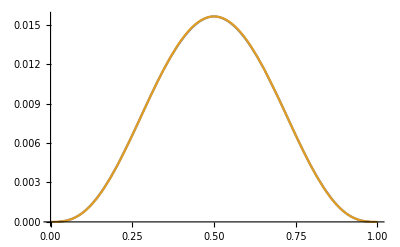

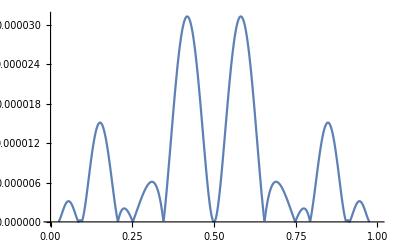

```mathematica
Clear[f,x,a,b,d];
n=7;
Do[x[k]=Sin[k*Pi/(2*n)]^2,{k,0,n}];
a=x[0];b=x[n];
f[t_]:=t^3*(1-t)^3;
Do[
coeff[-1,k]=1/(x[k]-x[k-1]);
coeff[0,k]=2*(1/(x[k+1]-x[k])+1/(x[k]-x[k-1]));
coeff[1,k]=1/(x[k+1]-x[k]);
freecoeff[k]=3*(f[x[k]]-f[x[k-1]])/(x[k]-x[k-1])^2+3*(f[x[k+1]]-f[x[k]])/(x[k+1]-x[k])^2,
{k,1,n-1}
];
coeff[0,1]=N[coeff[0,1]];
freecoeff[1]=N[freecoeff[1]];
s[0]=D[f[t],t]/.t->a;
s[n]=D[f[t],t]/.t->b;
freecoeff[1]=freecoeff[1]-s[0]/(x[1]-x[0]);
freecoeff[n-1]=freecoeff[n-1]-s[n]/(x[n]-x[n-1]);
Print[coeff[-1,1],coeff[0,1],coeff[1,1]];
Print[coeff[-1,2],coeff[0,2],coeff[1,2]];
sol=TridiagonalSolve[coeff,Table[freecoeff[k],{k,n-1}]];
sol//MatrixForm
Do[d[k]=sol[[k]],{k,1,n-1}];
Do[p[k_,t_]:=f[x[k]]+d[k]*(t-x[k])+((f[x[k+1]]-f[x[k]])/(x[k+1]-x[k])-d[k])/(x[k+1]-x[k])*(t-x[k])^2+(d[k+1]-2*(f[x[k+1]]-f[x[k]])/(x[k+1]-x[k])+d[k])/(x[k+1]-x[k])^2*(t-x[k])^2*(t-x[k+1]),
{k,0,n-1}
];
S[t_]:=Piecewise[Table[{p[k,t],t≥x[k]&&t≤x[k+1]},{k,0,n-1}]];
Plot[{S[t],f[t]},{t,a,b}]
Plot[Abs[f[t]-S[t]],{t,a,b}]
```